# ИДЗ 3

## Входные данные:

```mathematica
data={{"Вар","L1,Гн","L2,Гн","С1,Ф","С2,Ф","R1,Ом","R2,Ом","R3,Ом","R4,Ом","Количество отсчетов N (элементов массива)","Время между соседними отсчетами (δt), c","Контакты выхода","Номер гармоники","Файл сигнала"},{2,13.0678298352968,0.452099107439777,1.08320560443583*^-05,1.37999252996998*^-05,102.616603541089,30.152506879787,1080.99014737588,502.721830157102,8192,0.0196349540849362,"5 и 6",2,"2.txt"}};

table=Grid[data,Frame->All,Alignment->Center,Background->{{LightBlue,None},{LightYellow,None}}]
```

Вар | L1,Гн | L2,Гн | С1,Ф | С2,Ф | R1,Ом | R2,Ом | R3,Ом | R4,Ом | Количество отсчетов N (элементов массива) | Время между соседними отсчетами (δt), c | Контакты выхода | Номер гармоники | Файл сигнала
2 | 13.0678 | 0.452099 | 0.0000108321 | 0.0000137999 | 102.617 | 30.1525 | 1080.99 | 502.722 | 8192 | 0.019635 | 5 и 6 | 2 | 2.txt

```mathematica
Import["C:\\Users\\Danii\\OneDrive\\Изображения\\FOIT_scheme.png"]
```

-Graphics-

## Решение:

Для решения данной задачи необходимо

Рассчитать передаточную функцию системы H

Построить АЧХ передаточной функции

Выполнить дискретное преобразование Фурье для построения спектра сигнала

#### Начальные значения переменных

```mathematica
L1=SetPrecision[13.0678298352968,13];
L2=SetPrecision[0.452099107439777,13];
C1=SetPrecision[1.08320560443583*^-05,13];
C2=SetPrecision[1.37999252996998*^-05,13];
R1=SetPrecision[102.616603541089,13];
R2=SetPrecision[30.152506879787,13];
R3=SetPrecision[1080.99014737588,13];
R4=SetPrecision[502.721830157102,13];
dt=SetPrecision[0.0196349540849362,16];
N1=8192;
t=dt*N1;
```

#### Вычисление передаточной функции H:

Участок цепи 1-4:

```mathematica
Z1[w_] = R1 + I w L1;
```

Участок цепи 4-8 (правая ветвь):

```mathematica
Z2[w_]= R4 + 1 /( I w C2);
```

Участок цепи 4 - 8 (левая ветвь) :

```mathematica
Z3[w_]=1/(I w C1)+R2+I w L2+R3;
```

Сопротивление всего участка 4-8:

```mathematica
Zpar[w_] = Z2[w] Z3[w]/(Z2[w] + Z3[w]);
```

Сила тока в цепи:

```mathematica
I1[w_] = Uin/(Z1[w] + Zpar[w]);
```

Т.к. участок 1-2 и 4-8 соединены параллельно, то сила тока одинакова, отсюда можем вычислить падение напряжения на участке 4-8:

```mathematica
Upar[w_] = I1[w] Zpar[w];
```

Падение напряжения на ветвях участка с параллельным соединением одинаково, отсюда можем найти силу тока на левой ветви участка 4-8:

```mathematica
IparLeft[w_] = Upar[w] / Z3[w];
```

Тогда выходное напряжение на участке 5-6:

```mathematica
Uout[w_]=IparLeft[w]*R2;
```

Подставим в отношение для передаточной функции H:

```mathematica
H[w_] = Uout[w]/Uin ;
```

#### Построение графика АЧХ

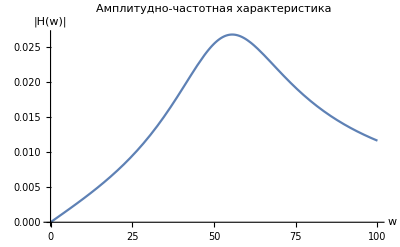

```mathematica
AChH = Plot[Abs@H[w],{w,0,100}, AxesLabel->{"w","|H(w)|"}, PlotLabel->"Амплитудно-частотная характеристика"]
```

#### Построение графика сигнала

Прочитаем сигнал из входного файла и поместим их в массив

```mathematica
signal = Flatten[Import["C:\\Users\\Danii\\OneDrive\\Документы\\foit\\2.txt", "Table"]];
signalTable = Table[{(i-1)*dt,signal[[i]]},{i,1,N1}];
```

Составим таблицу для отношения время-сигнал:

```mathematica
headers={"t","U(t)"};

table = Grid[Prepend[signalTable,headers],Frame->All,Alignment->Center,Background->{{LightBlue,None},{LightYellow,None}}];
table; (*убрать ";", чтобы посмотреть*)
```

Построим по данной таблице график:

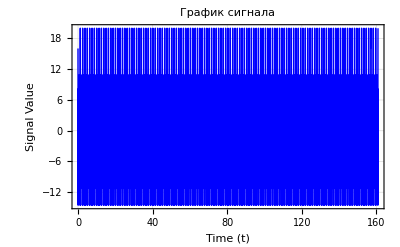

```mathematica
ListLinePlot[signalTable,FrameLabel->{"Time (t)","Signal Value"},PlotLabel->"График сигнала",Frame->True,GridLines->Automatic,PlotStyle->{Blue, Thin}]
```

#### Построение спектра

Для построения спектра выполним дискретное преобразование Фурье и

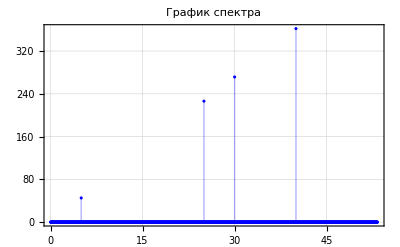

```mathematica
Fsig=Fourier[signal];
outN=Length@Fsig;
df=1/t;
FourierAbs=Table[{2 π df (i-1),Abs@Fsig[[i]]},{i,1,outN/6}];
ListPlot[FourierAbs,Filling->Axis,PlotRange->Full, PlotLabel->"График спектра",Frame->True,GridLines->Automatic,PlotStyle->{Blue, Thin}]
```

#### Нахождение коэффициента усиления для 2 гармоники

0.0094539108356

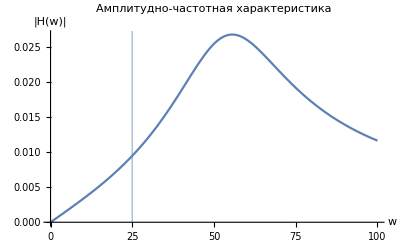

```mathematica
Abs@H[25]
Show[AChH, ListPlot[{{25, 0.5}}, Filling->Axis]]
```